```mathematica
m3a12[a_]:={{Cos[a],-Sin[a],0},{Sin[a],Cos[a],0},{0,0,1}};
```

```mathematica
m3a23[a_]:={{1,0,0},{0,Cos[a],-Sin[a]},{0,Sin[a],Cos[a]}};
```

```mathematica
m3a31[a_]:={{Cos[a],0,Sin[a]},{0,1,0},{-Sin[a],0,Cos[a]}};
```

```mathematica
mm3[a12_,a23_,a31_]:=m3a12[a12].m3a23[a23].m3a31[a31]
```

```mathematica
mm3[x,y,z]//MatrixForm
```

(Cos[x] Cos[z]-Sin[x] Sin[y] Sin[z] | -Cos[y] Sin[x] | Cos[z] Sin[x] Sin[y]+Cos[x] Sin[z]
Cos[z] Sin[x]+Cos[x] Sin[y] Sin[z] | Cos[x] Cos[y] | -Cos[x] Cos[z] Sin[y]+Sin[x] Sin[z]
-Cos[y] Sin[z] | Sin[y] | Cos[y] Cos[z])

```mathematica
rs3[m_,i_,x_,y_,z_]:=Sum[Abs[mm3[x,y,z][[i]][[j]]],{j,m}]
```

```mathematica
rs3[1,1,x,y,z]
```

Abs[Cos[x] Cos[z]-Sin[x] Sin[y] Sin[z]]

```mathematica
mrs3[m_,n_,x_,y_,z_]:=Max[MapThread[rs3,{Table[m,{i,n}],Range[n],Table[x,{i,n}],Table[y,{i,n}],Table[z,{i,n}]}]]
```

```mathematica
mrs3[2,3,x,y,z]
```

Max[Abs[Sin[y]]+Abs[Cos[y] Sin[z]],Abs[Cos[x] Cos[y]]+Abs[Cos[z] Sin[x]+Cos[x] Sin[y] Sin[z]],Abs[Cos[y] Sin[x]]+Abs[Cos[x] Cos[z]-Sin[x] Sin[y] Sin[z]]]

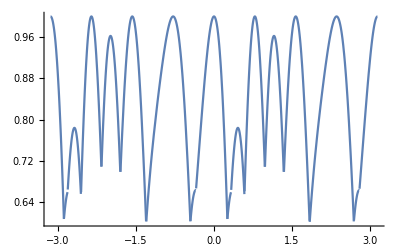

```mathematica
Plot[mrs3[1,3,x,2x,3x],{x,-Pi,Pi}]
```

```mathematica
m2a12[a_]:={{Cos[a],-Sin[a]},{Sin[a],Cos[a]}};
```

```mathematica
mm2[a12_]:=m2a12[a12]
```

```mathematica
mm2[x]//MatrixForm
```

(Cos[x] | -Sin[x]
Sin[x] | Cos[x])

```mathematica
rs2[m_,i_,x_]:=Sum[Abs[mm2[x][[i]][[j]]],{j,m}]
```

```mathematica
rs2[1,1,x]
```

Abs[Cos[x]]

```mathematica
mrs2[m_,n_,x_]:=Max[MapThread[rs2,{Table[m,{i,n}],Range[n],Table[x,{i,n}]}]]
```

```mathematica
mrs2[1,2,x]
```

Max[Abs[Cos[x]],Abs[Sin[x]]]

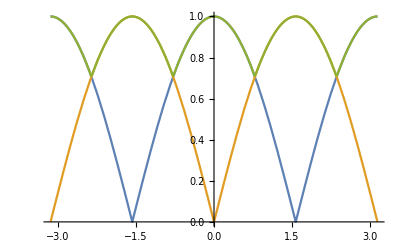

```mathematica
Plot[{rs2[1,1,x],rs2[1,2,x],mrs2[1,2,x]},{x,-Pi,Pi}]
```

```mathematica
mrs2[1,2,x]
```

Max[Abs[Cos[x]],Abs[Sin[x]]]

```mathematica
mrs3[1,3,x,y,z]
```

Max[Abs[Cos[y] Sin[z]],Abs[Cos[z] Sin[x]+Cos[x] Sin[y] Sin[z]],Abs[Cos[x] Cos[z]-Sin[x] Sin[y] Sin[z]]]

```mathematica
mrs3[1,3,x,y,0]
```

Max[0,Abs[Cos[x]],Abs[Sin[x]]]

```mathematica
mrs3[1,3,x,0,z]
```

Max[Abs[Cos[x] Cos[z]],Abs[Cos[z] Sin[x]],Abs[Sin[z]]]

```mathematica
mrs3[1,3,0,y,z]
```

Max[Abs[Cos[z]],Abs[Cos[y] Sin[z]],Abs[Sin[y] Sin[z]]]

```mathematica
mrs3[2,3,x,y,z]
```

Max[Abs[Sin[y]]+Abs[Cos[y] Sin[z]],Abs[Cos[x] Cos[y]]+Abs[Cos[z] Sin[x]+Cos[x] Sin[y] Sin[z]],Abs[Cos[y] Sin[x]]+Abs[Cos[x] Cos[z]-Sin[x] Sin[y] Sin[z]]]

```mathematica
mrs3[2,3,x,y,0]
```

Max[Abs[Cos[x] Cos[y]]+Abs[Sin[x]],Abs[Cos[x]]+Abs[Cos[y] Sin[x]],Abs[Sin[y]]]

```mathematica
mrs3[2,3,x,0,z]
```

Max[Abs[Cos[x] Cos[z]]+Abs[Sin[x]],Abs[Cos[x]]+Abs[Cos[z] Sin[x]],Abs[Sin[z]]]

```mathematica
Plot3D[mrs3[2,3,x,0,z],{x,-Pi/2,Pi/2},{z,-Pi/2,Pi/2},PlotPoints->50]
```

-Graphics3D-

```mathematica
FindMinimum[mrs3[2,3,x,0,z],{{x,0.78461},{z,1.24}},WorkingPrecision->10,AccuracyGoal->40,PrecisionGoal->40]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than 10. digits of working precision to meet these tolerances.

{0.9429328087,{x→0.78461,z→1.231330912}}

```mathematica
N[Sqrt[8/9]]
```

0.942809

```mathematica
Plot3D[{Abs[Sin[z]],Abs[Cos[x]]+Abs[Sin[x]Cos[z]],Abs[Sin[x]]+Abs[Cos[x]Cos[z]]},{x,-Pi/2,Pi/2},{z,-Pi/2,Pi/2},PlotPoints->50]
```

-Graphics3D-

```mathematica
srs2[m_,i_,x_]:=Sum[mm2[x][[i]][[j]],{j,m}]
```

```mathematica
srs3[m_,i_,x_,y_,z_]:=Sum[mm3[x,y,z][[i]][[j]],{j,m}]
```

```mathematica
ContourPlot3D[{rs3[1,1,x,y,z]==rs3[1,2,x,y,z],rs3[1,1,x,y,z]==rs3[1,3,x,y,z]},{x,-Pi/2,Pi/2},{y,-Pi/2,Pi/2},{z,-Pi/2,Pi/2},Mesh->None,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
ContourPlot3D[{Abs[Sqrt[1-y^2]z ]== Abs[x Sqrt[1-z^2]+Sqrt[1-x^2]y z],Abs[Sqrt[1-y^2]z] ==Abs[Sqrt[1-x^2]Sqrt[1-z^2]-x y z],y==0},{x,-1,1},{y,-1,1},{z,-1,1},Mesh->None,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
ContourPlot3D[{srs3[1,1,x,y,z]==0},{x,-Pi,Pi},{y,-Pi,Pi},{z,-Pi,Pi},Mesh->None,AxesLabel->Automatic]
```

-Graphics3D-